Engineering Applications of Stochastic Processes Notebook
Created by: Karthikeyan Palanikumar

Summation:

```mathematica
∑_(i=1)^∞ ∑_(j=1)^i 1/(j^2(i+1)^2)
```

π^4/120

```mathematica
∑_(i=1)^∞ 1/i^6
```

π^6/945

Integration:

```mathematica
∫_0^1500 y * 0.001* Exp[-0.001*y]ⅆy+∫_1500^∞ 1500*0.001* Exp[-0.001*y]ⅆy
```

776.87

Definite Integral:

```mathematica
Integrate[1/(x^3+1),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

Indefinite Integral:

```mathematica
Integrate[x^2+Sin[x],x]
```

x^3/3-Cos[x]

Binomial Random Variables:

```mathematica
b[n_,t_,p_] := Binomial[t,n]* p^n * (1-p)^(t-n)
```

```mathematica
b[6,10,3.4/5.8]
```

0.249838

```mathematica
B[n_,t_,p_] := ∑_(i=0)^n Binomial[t,i]* p^i * (1-p)^(t-i)
```

```mathematica
B[1,2,0.2]
```

0.96

```mathematica
b[0,3,0.2]/B[1,3,0.2]
```

0.571429

Negative Binomial Random Variables:

b^-1[n,s,p]

```mathematica
c[n_,s_,p_] := Binomial[s-1,n-1]* p^n * (1-p)^(s-n)
```

```mathematica
c[4,150,0.05]
```

0.0018886

B^-1[n,s,p]

```mathematica
d[n_,s_,p_] := ∑_(i=n)^s Binomial[i-1,n-1]* p^n * (1-p)^(i-n)
```

```mathematica
d[3,27,0.12]
```

0.644707

Single Sampling Plan:

OC(p)= B(c,n,p)

```mathematica
B[2,110,0.03]
```

0.355449

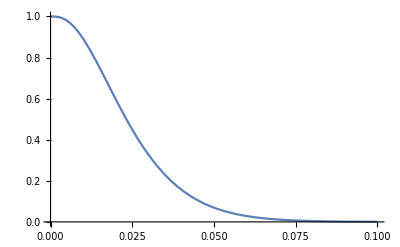

```mathematica
Plot[B[2,115,p],{p,0,0.1}]
```

Double Sampling Plans without Curtailment:

OC(p)= B[c1,n1,p]+ ∑_(y=c1+1)^c2 B[c2-y,n2,p]*b[y,n1,p]

```mathematica
B[0,40,0.01]+ ∑_(y=0+1)^2 B[2-y,80,0.01]*b[y,40,0.01]
```

0.911506

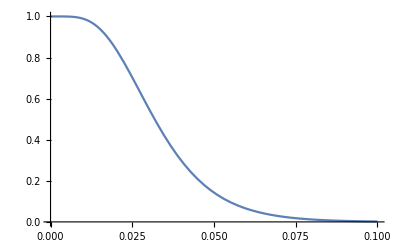

```mathematica
Plot[B[2,100,p]+ ∑_(y=2+1)^5 B[5-y,100,p]*b[y,100,p],{p,0,0.1}]
```

ASN(p)= n1+n2*(B[c2,n1,p]-B[c1,n1,p])

```mathematica
40+80*(B[2,40,0.025]-B[0,40,0.025])
```

84.7055

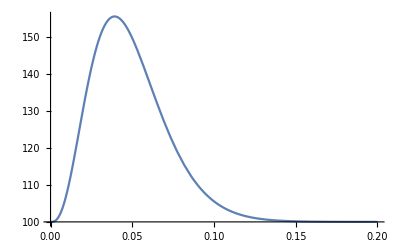

```mathematica
p1=Plot[100+100 (161700 (1-p)^97 p^3+3921225 (1-p)^96 p^4+75287520 (1-p)^95 p^5),{p,0,0.2}]
```

Double Sampling Plans with Curtailment:

OC(p)= B[c1,n1,p]+ ∑_(y=c1+1)^c2 B[c2-y,n2,p]*b[y,n1,p]

```mathematica
B[0,40,0.01]+ ∑_(y=0+1)^2 B[2-y,80,0.01]*b[y,40,0.01]
```

0.911506

ASN(p)= n1+ ∑_(y=c1+1)^c2 (n2*B[c2-y,n2,p]+∑_(s=c2-y+1)^n2 s*b^-1[c2-y+1,s,p])*b[y,n1,p]

```mathematica
40+ ∑_(y=0+1)^2 (80*B[2-y,80,0.025]+∑_(s=2-y+1)^80 s*c[2-y+1,s,0.025])*b[y,40,0.025]
```

68.3063

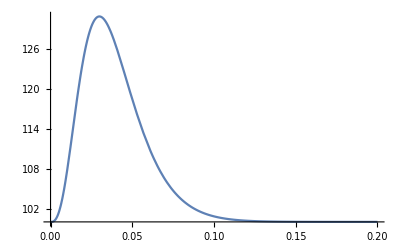

```mathematica
p2=Plot[100+ ∑_(y=2+1)^5 (100*B[5-y,100,p]+∑_(s=5-y+1)^100 s*c[5-y+1,s,p])*b[y,100,p],{p,0,0.2}]
```

```mathematica
Show[p1,p2]
```

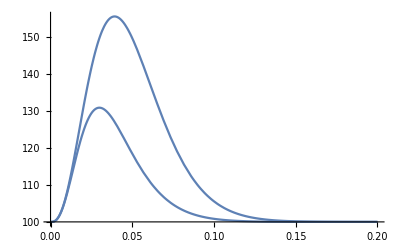

Single Sample Rectifying Inspection Plan
AOQ(p)=((m-n)×p×B[c,n,p])/m

```mathematica
((3000-100)×0.005×B[1,100,0.005])/3000
```

0.00439919

AFI(p)=(n+(m-n)×(1-B[c,n,p]))/m

```mathematica
(110+(2750-110)×(1-B[2,110,0.025]))/2750
```

0.540006

Plotting AOQ function:

```mathematica
AOQ[m_,n_,p_,c_]:=((m-n)×p×B[c,n,p])/m
AOQ[2750,110,p,2]
```

24/25 p ((1-p)^110+110 (1-p)^109 p+5995 (1-p)^108 p^2)

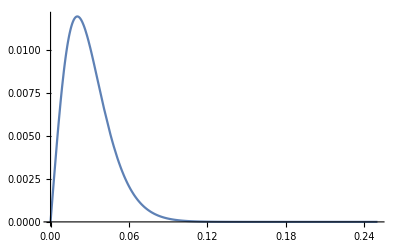

```mathematica
Plot[24/25 p ((1-p)^110+110 (1-p)^109 p+5995 (1-p)^108 p^2),{p,0,0.25}]
```

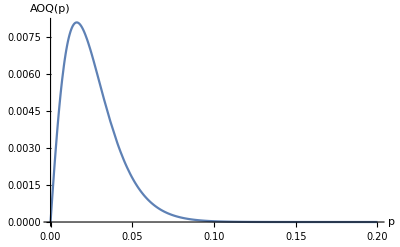

```mathematica
Plot[29/30 p ((1-p)^100+100 (1-p)^99 p),{p,0,0.2},AxesLabel->{p,AOQ[p]}]
```

```mathematica
NMaximize[AOQ[2750,110,p,2],p]
```

{0.0119518,{p→0.0204855}}

Plot AFI Function:

```mathematica
AFI[n_,m_,c_,p_]:=(n+(m-n)×(1-B[c,n,p]))/m
```

```mathematica
AFI[110,2750,2,0.025]
```

0.540006

```mathematica
AFI[110,2750,2,p]
```

(110+2640 (1-(1-p)^110-110 (1-p)^109 p-5995 (1-p)^108 p^2))/2750

```mathematica
NMaximize[AFI[110,2750,2,p],{p}]
```

{1.,{p→1.15857}}

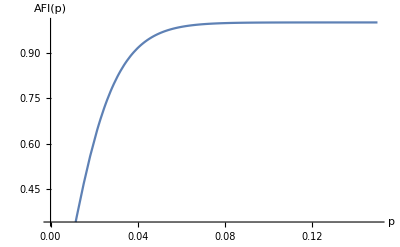

```mathematica
Plot[(100+2900 (1-(1-p)^100-100 (1-p)^99 p))/3000,{p,0,0.15},AxesLabel->{p,AFI[p]}]
```

Continuous Sampling Plan(CSP-1)

u(p)=  (1-(1-p)^i)/(p×(1-p)^i); v(p)= 1/(f×p)

```mathematica
(1-(1-p)^i)/(p×(1-p)^i)
```

```mathematica
1/(f×p)
```

AOQ(p)=((1-f)×p×1/(f×p))/((1-(1-p)^i)/(p×(1-p)^i)+1/(f×p));AFI(p)= ((1-(1-p)^i)/(p×(1-p)^i)+f× 1/(f×p))/((1-(1-p)^i)/(p×(1-p)^i)+1/(f×p))

```mathematica
((1-0.2)×p×1/(0.2×p))/((1-(1-p)^50)/(p×(1-p)^50)+1/(0.2×p))
```

4./(5./p+(1-(1-p)^50)/((1-p)^50 p))

```mathematica
((1-(1-p)^50)/(p×(1-p)^50)+0.2× 1/(0.2×p))/((1-(1-p)^50)/(p×(1-p)^50)+1/(0.2×p))
```

(1./p+(1-(1-p)^50)/((1-p)^50 p))/(5./p+(1-(1-p)^50)/((1-p)^50 p))

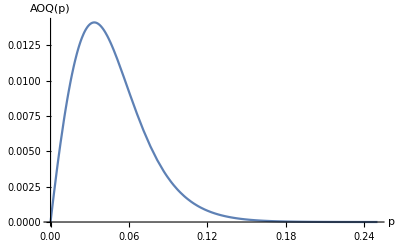

```mathematica
Plot[4./(5./p+(1-(1-p)^50)/((1-p)^50 p)),{p,0,0.25},AxesLabel->{p,AOQ[p]}]
```

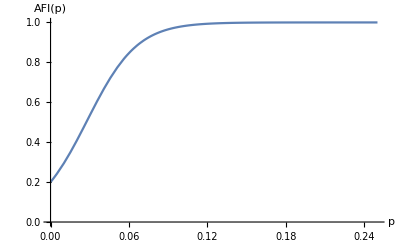

```mathematica
Plot[(1./p+(1-(1-p)^50)/((1-p)^50 p))/(5./p+(1-(1-p)^50)/((1-p)^50 p)),{p,0,0.25},PlotRange->{{0,0.25},{0,1}},AxesLabel->{p,AFI[p]}]
```

Poisson Process:

Pr(N(t)=n)= p[n_,ℷt_]= (ⅇ^-ℷt×(ℷt)^n)/(n!)

```mathematica
p[n_,ℷt_]:= (ⅇ^-ℷt×(ℷt)^n)/(n!)
```

```mathematica
p[4,0.005*750]
```

0.19378

```mathematica
N[9/(2 ⅇ^3),2]
```

0.22

Pr(N(t)<=n)= P[n_,ℷt_]= ∑_(i=0)^n (ⅇ^-ℷt×(ℷt)^i)/(i!)

```mathematica
P[n_,ℷt_]:=∑_(i=0)^n (ⅇ^-ℷt×(ℷt)^i)/(i!)
```

```mathematica
P[3,0.005*750]
```

0.483767

```mathematica
N[899/(5 ⅇ^6),2]
```

0.45

```mathematica
N[1-2101/(7 ⅇ^6),2]
```

0.26

Modelling Arrival Times:
Pr(S(n)<=s)= 1-∑_(i=0)^(n-1) (ⅇ^-ℷs×(ℷs)^i)/(i!)

```mathematica
Q[n_,ℷs_]:=1-∑_(i=0)^(n-1) (ⅇ^-ℷs×(ℷs)^i)/(i!) 
Q[3,1.2*2]
```

0.430291

Pr(S(n)>s) = ∑_(i=0)^(n-1) (ⅇ^-ℷs×(ℷs)^i)/(i!)

```mathematica
R[n_,ℷs_]:=∑_(i=0)^(n-1) (ⅇ^-ℷs×(ℷs)^i)/(i!)
R[1,5.8*0.1]
```

0.559898

Competing Poisson Process:

∑_(i=n)^(n+m-1) b[i,n+m-1,λ1/(λ1+λ2)]

```mathematica
∑_(i=8)^(8+4-1) b[i,8+4-1,3.4/(3.4+1.1)]
```

0.728482

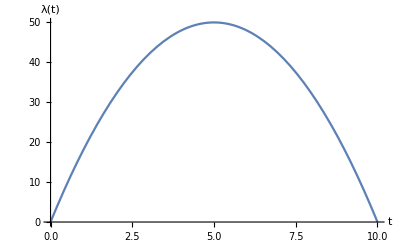

```mathematica
Plot[50-2(t-5)^2,{t,0,10},AxesLabel->{t,λ[t]}]
```

Non-Homogeneous Poisson Process
λ(t)= ∫_0^t λ(u)ⅆu

```mathematica
∫_0^4 (50-2(u-5)^2)ⅆu
```

352/3

```mathematica
N[352/3]
```

117.333

```mathematica
∫_4^6 (t+4) ⅆt + ∫_6^9 (22-2t)ⅆt
```

39

CFR Repairable System Models:
Continuous-time Markov Chain Model:

Availability Function,

```mathematica
A[μ_,λ_,t_]:= μ/(λ+μ)+λ/(λ+μ)*ⅇ^(-(λ+μ)t)
A[1/50,1/400,120]
```

8/9+1/(9 ⅇ^(27/10))

```mathematica
N[8/9+1/(9 ⅇ^(27/10)),3]
```

0.896

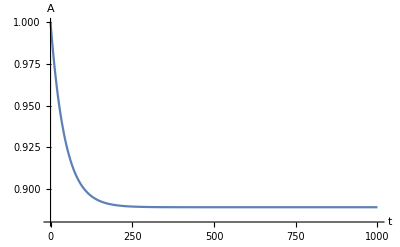

```mathematica
Plot[8/9+1/9 ⅇ^(-9 t/400),{t,0,1000},PlotRange->{0.88,1},AxesLabel->{t,A}]
```

```mathematica
N[25/26+1/(26 ⅇ^(39/25)),3]
```

0.97

Average Availability Function,

```mathematica
Subscript[A, avg][μ_,λ_,t_]:= μ/(λ+μ)+λ/((λ+μ)^2*t)*(1-ⅇ^(-(λ+μ)t))
Subscript[A, avg][1/50,1/400,120]
```

8/9+10/243 (1-1/ⅇ^(27/10))

```mathematica
N[8/9+10/243 (1-1/ⅇ^(27/10)),3]
```

0.927

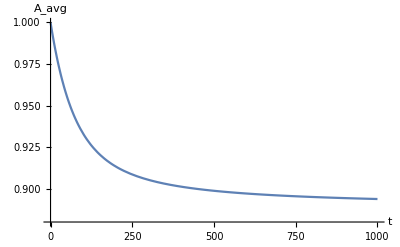

```mathematica
Plot[8/9+(400 (1-ⅇ^(-9 t/400)))/(81 t),{t,0,1000},PlotRange->{0.88,1},AxesLabel->{t,Subscript[A, avg]}]
```

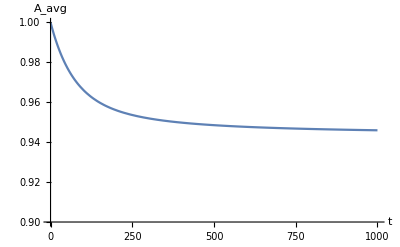

```mathematica
Plot[50/53+(7200 (1-ⅇ^(-53 t/2400)))/(2809 t),{t,0,1000},PlotRange->{0.90,1},AxesLabel->{t,Subscript[A, avg]}]
```

```mathematica
N[25/26+(25 (1-1/ⅇ^(39/25)))/1014,2]
```

0.98

Age Replacement Model:
Availability based on optimal age-based PM policy:
A[τ_]:=(∫_0^τ (t*f[t]ⅆt)+(τ*R[τ]))/(∫_0^τ (t*f[t]ⅆt)+(τ*R[τ])+(D_CM*F[τ]+ D_PM*R[τ]))

```mathematica
R[t_]:=Exp[-(t/η)^β];
F[t_]:= 1-R[t];
f[t_]:=F'[t];
β=2.15; η=1600; Subscript[D, CM]= 180; Subscript[D, PM]=12;
A[τ_]:=(∫_0^τ (t*f[t]ⅆt)+(τ*R[τ]))/(∫_0^τ (t*f[t]ⅆt)+(τ*R[τ])+(Subscript[D, CM]*F[τ]+ Subscript[D, PM]*R[τ]))
```

```mathematica
A[441.4]
```

0.951172

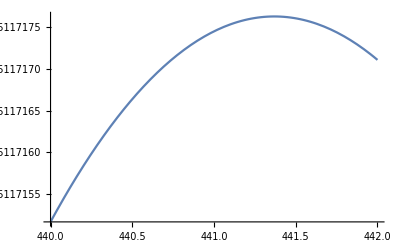

```mathematica
Plot[(1416.9734246232488+ⅇ^(-1.2916416397452518*^-7 τ^2.15) τ-(1599.999999999998 τ^3.15 Gamma[1.4651162790697674,1.2916416397452518*^-7 τ^2.15])/((τ^2.15)^1.4651162790697674))/(1416.9734246232488+12 ⅇ^(-1.2916416397452518*^-7 τ^2.15)+180 (1-ⅇ^(-1.2916416397452518*^-7 τ^2.15))+ⅇ^(-1.2916416397452518*^-7 τ^2.15) τ-(1599.999999999998 τ^3.15 Gamma[1.4651162790697674,1.2916416397452518*^-7 τ^2.15])/((τ^2.15)^1.4651162790697674)),{τ,440,442}]
```

```mathematica
Gamma[(1/2.15)+1]
```

0.885608